```mathematica
Import["https://qtechtheory.org/questlink.m"]
SetDirectory[NotebookDirectory[]]
CreateLocalQuESTEnv["quest_link_cpu"];
```

/home/cica/postox/papers/chemistry-code/vqe

## Convert questlink gates format to quantikz

The printed decimal

```mathematica
decimal=3;
```

## LiH, 12 qubits

```mathematica
ResLiH={{{Subscript[Rx, 10][Subscript[θ, 117]],Subscript[Rx, 3][Subscript[θ, 204]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 173]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 129]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 108]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 206]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[Rz, 3][Subscript[θ, 180]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 104]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 194]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 235]]],Subscript[C, 1][Subscript[Rx, 5][Subscript[θ, 207]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 232]]],Subscript[Rz, 10][Subscript[θ, 223]],Subscript[C, 5][Subscript[Rz, 8][Subscript[θ, 211]]],Subscript[Ry, 10][Subscript[θ, 155]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 228]]],Subscript[Rx, 5][Subscript[θ, 236]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 181]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 185]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 188]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 197]]]},<|Subscript[θ, 30]->3.141711789896502,Subscript[θ, 99]->3.1390782883054187,Subscript[θ, 104]->4.235954625354078,Subscript[θ, 108]->-1.7684845653108956,Subscript[θ, 117]->0.2979748735187607,Subscript[θ, 129]->4.7092435090226195,Subscript[θ, 155]->-0.9815416223263715,Subscript[θ, 173]->-3.141592381755277,Subscript[θ, 180]->-1.5691665458545887,Subscript[θ, 181]->3.141589825634101,Subscript[θ, 185]->3.141590667955607,Subscript[θ, 188]->-3.1601000732067854,Subscript[θ, 194]->3.1533846075595338,Subscript[θ, 197]->3.1443501803768825,Subscript[θ, 204]->-0.33924862645881143,Subscript[θ, 206]->0.3374978059471821,Subscript[θ, 207]->1.506934642901632,Subscript[θ, 211]->0.6529305223145572,Subscript[θ, 223]->-1.5707597559343176,Subscript[θ, 228]->-0.3375434132731413,Subscript[θ, 232]->-0.06185151118739833,Subscript[θ, 235]->-0.9818502855537647,Subscript[θ, 236]->-1.509699784387328|>,<|"ansatz"->{{},{Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 9]]],Subscript[C, 0][Subscript[Rx, 4][Subscript[θ, 22]]],Subscript[C, 1][Subscript[Rx, 10][Subscript[θ, 24]]],Subscript[Ry, 5][Subscript[θ, 16]],Subscript[Rx, 4][Subscript[θ, 23]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 83]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]]},{Subscript[Rx, 10][Subscript[θ, 117]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 129]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 108]]],Subscript[C, 5][Subscript[Rz, 10][Subscript[θ, 111]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 104]]]},{Subscript[Rx, 10][Subscript[θ, 117]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 173]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 129]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 108]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 104]]],Subscript[Rz, 3][Subscript[θ, 180]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 151]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 194]]],Subscript[Ry, 10][Subscript[θ, 155]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 171]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 181]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 185]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 188]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 197]]]},{Subscript[Rx, 10][Subscript[θ, 117]],Subscript[Rx, 3][Subscript[θ, 204]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 173]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 129]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 108]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 206]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[Rz, 3][Subscript[θ, 180]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 104]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 194]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 235]]],Subscript[C, 1][Subscript[Rx, 5][Subscript[θ, 207]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 232]]],Subscript[Rz, 10][Subscript[θ, 223]],Subscript[C, 5][Subscript[Rz, 8][Subscript[θ, 211]]],Subscript[Ry, 10][Subscript[θ, 155]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 228]]],Subscript[Rx, 5][Subscript[θ, 236]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 181]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 185]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 188]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 197]]]},{Subscript[Rx, 10][Subscript[θ, 117]],Subscript[Rx, 3][Subscript[θ, 204]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 173]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 129]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 108]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 30]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 206]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[Rz, 3][Subscript[θ, 180]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 104]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 194]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 235]]],Subscript[C, 1][Subscript[Rx, 5][Subscript[θ, 207]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 232]]],Subscript[Rz, 10][Subscript[θ, 223]],Subscript[C, 5][Subscript[Rz, 8][Subscript[θ, 211]]],Subscript[Ry, 10][Subscript[θ, 155]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 228]]],Subscript[Rx, 5][Subscript[θ, 236]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 181]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 185]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 188]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 197]]]}},"θvars"->{<||>,<|Subscript[θ, 9]->-0.3829175338421037,Subscript[θ, 16]->0.3827540903587453,Subscript[θ, 22]->0.16351142140222635,Subscript[θ, 23]->-0.16327330166875245,Subscript[θ, 24]->-0.23762611835260483,Subscript[θ, 30]->3.141661424702561,Subscript[θ, 83]->3.1415756513005335,Subscript[θ, 99]->3.1415931992022488|>,<|Subscript[θ, 30]->3.1415926535897936,Subscript[θ, 99]->3.1415742422659463,Subscript[θ, 104]->3.13178696797533,Subscript[θ, 108]->-3.160154962815924,Subscript[θ, 111]->3.1419079689152887,Subscript[θ, 117]->0.2595735570311816,Subscript[θ, 129]->5.457129127043042|>,<|Subscript[θ, 30]->3.141546338452161,Subscript[θ, 99]->3.1415926553394873,Subscript[θ, 104]->3.141592936800313,Subscript[θ, 108]->-3.1415918851169398,Subscript[θ, 117]->0.2904083676604961,Subscript[θ, 129]->5.407285595535527,Subscript[θ, 151]->0.876462483452499,Subscript[θ, 155]->-0.8764269766333546,Subscript[θ, 171]->2.8949697562400454,Subscript[θ, 173]->-3.1415926536415024,Subscript[θ, 180]->-1.437156354008911,Subscript[θ, 181]->3.141592653810172,Subscript[θ, 185]->3.1415926537705414,Subscript[θ, 188]->-3.153898480257826,Subscript[θ, 194]->3.1300744737667046,Subscript[θ, 197]->3.1447922899151783|>,<|Subscript[θ, 30]->3.1422583321050075,Subscript[θ, 99]->3.1391329359233198,Subscript[θ, 104]->4.233082875901434,Subscript[θ, 108]->-1.7699252668665684,Subscript[θ, 117]->0.2976686343931374,Subscript[θ, 129]->4.711216399803328,Subscript[θ, 155]->-0.981544236854908,Subscript[θ, 173]->-3.1415919934287815,Subscript[θ, 180]->-1.569267525944522,Subscript[θ, 181]->3.14158799590305,Subscript[θ, 185]->3.141589281232151,Subscript[θ, 188]->-3.1603096213349957,Subscript[θ, 194]->3.15342257575471,Subscript[θ, 197]->3.144373443852869,Subscript[θ, 204]->-0.34083546642559814,Subscript[θ, 206]->0.3365741751949142,Subscript[θ, 207]->1.5066994739795894,Subscript[θ, 211]->0.6512703209354266,Subscript[θ, 223]->-1.570704650274721,Subscript[θ, 228]->-0.33913556696953345,Subscript[θ, 232]->-0.06174762407945452,Subscript[θ, 235]->-0.981813217658464,Subscript[θ, 236]->-1.5093014138446768|>,<|Subscript[θ, 30]->3.141711789896502,Subscript[θ, 99]->3.1390782883054187,Subscript[θ, 104]->4.235954625354078,Subscript[θ, 108]->-1.7684845653108956,Subscript[θ, 117]->0.2979748735187607,Subscript[θ, 129]->4.7092435090226195,Subscript[θ, 155]->-0.9815416223263715,Subscript[θ, 173]->-3.141592381755277,Subscript[θ, 180]->-1.5691665458545887,Subscript[θ, 181]->3.141589825634101,Subscript[θ, 185]->3.141590667955607,Subscript[θ, 188]->-3.1601000732067854,Subscript[θ, 194]->3.1533846075595338,Subscript[θ, 197]->3.1443501803768825,Subscript[θ, 204]->-0.33924862645881143,Subscript[θ, 206]->0.3374978059471821,Subscript[θ, 207]->1.506934642901632,Subscript[θ, 211]->0.6529305223145572,Subscript[θ, 223]->-1.5707597559343176,Subscript[θ, 228]->-0.3375434132731413,Subscript[θ, 232]->-0.06185151118739833,Subscript[θ, 235]->-0.9818502855537647,Subscript[θ, 236]->-1.509699784387328|>},"E"->{-7.861358505265061,-7.876095442835334,-7.878039340461649,-7.880433315369665,-7.880733614941139,-7.880733834997171},"idx"->{1,101,151,201,251,251}|>,7112,{},{0,102,56,69}},{{Subscript[Rx, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 10]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 133]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 18]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 22]]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 59]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 36]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 50]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 66]]],Subscript[Ry, 10][Subscript[θ, 51]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 87]]]},<|Subscript[θ, 10]->3.1415926535897936,Subscript[θ, 18]->-1.565069391119124,Subscript[θ, 22]->2.319552438012357,Subscript[θ, 36]->-3.141592653589793,Subscript[θ, 50]->-3.141592653589793,Subscript[θ, 51]->3.141592653589793,Subscript[θ, 59]->-3.1415926535901852,Subscript[θ, 66]->3.141592653589793,Subscript[θ, 87]->3.141592653589793,Subscript[θ, 116]->-2.3269077142849857,Subscript[θ, 119]->1.5652163937364485,Subscript[θ, 133]->0.2839190358472256|>,<|"ansatz"->{{},{Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 10]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 22]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 18]]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 59]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 36]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 50]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 66]]],Subscript[Ry, 10][Subscript[θ, 51]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 87]]],Subscript[Rz, 3][Subscript[θ, 99]]},{Subscript[Rx, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 10]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 133]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 18]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 22]]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 59]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 36]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 50]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 66]]],Subscript[Ry, 10][Subscript[θ, 51]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 87]]]},{Subscript[Rx, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 10]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 133]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 18]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 22]]],Subscript[C, 1][Subscript[Ry, 6][Subscript[θ, 59]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 36]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 50]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 66]]],Subscript[Ry, 10][Subscript[θ, 51]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 87]]]}},"θvars"->{<||>,<|Subscript[θ, 10]->3.1415926532368394,Subscript[θ, 18]->-0.23784278803266184,Subscript[θ, 22]->-0.014359775714223777,Subscript[θ, 36]->-3.1415926535897225,Subscript[θ, 50]->-3.1415926535902647,Subscript[θ, 51]->3.1415926535902616,Subscript[θ, 59]->-3.14159263848463,Subscript[θ, 66]->3.1415926535897265,Subscript[θ, 87]->3.14159265359016,Subscript[θ, 99]->1.568596063688777|>,<|Subscript[θ, 10]->3.1415926535897936,Subscript[θ, 18]->-1.565069391119124,Subscript[θ, 22]->2.319552438012357,Subscript[θ, 36]->-3.141592653589793,Subscript[θ, 50]->-3.141592653589793,Subscript[θ, 51]->3.141592653589793,Subscript[θ, 59]->-3.1415926535901852,Subscript[θ, 66]->3.141592653589793,Subscript[θ, 87]->3.141592653589793,Subscript[θ, 116]->-2.3269077142849857,Subscript[θ, 119]->1.5652163937364485,Subscript[θ, 133]->0.2839190358472256|>,<|Subscript[θ, 10]->3.1415926535897936,Subscript[θ, 18]->-1.565069391119124,Subscript[θ, 22]->2.319552438012357,Subscript[θ, 36]->-3.141592653589793,Subscript[θ, 50]->-3.141592653589793,Subscript[θ, 51]->3.141592653589793,Subscript[θ, 59]->-3.1415926535901852,Subscript[θ, 66]->3.141592653589793,Subscript[θ, 87]->3.141592653589793,Subscript[θ, 116]->-2.3269077142849857,Subscript[θ, 119]->1.5652163937364485,Subscript[θ, 133]->0.2839190358472256|>},"E"->{-7.861358505265061,-7.876115106516198,-7.878039255942735,-7.878039255942735},"idx"->{1,101,151,151}|>,2938,{4},{0,28,29,81}},{{Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 282]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 285]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 295]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 297]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 228]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 247]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 328]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 333]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 335]]],Subscript[Rz, 3][Subscript[θ, 340]],Subscript[Rx, 5][Subscript[θ, 349]],Subscript[C, 3][Subscript[Rz, 4][Subscript[θ, 375]]],Subscript[C, 2][Subscript[Rx, 5][Subscript[θ, 363]]],Subscript[Rx, 5][Subscript[θ, 369]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 377]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 378]]]},<|Subscript[θ, 107]->3.5089714305812496,Subscript[θ, 120]->-3.1415925901578,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 130]->3.141592653589793,Subscript[θ, 148]->3.143049901771186,Subscript[θ, 173]->-0.2348359803895058,Subscript[θ, 176]->3.1415926124737936,Subscript[θ, 189]->-3.141592622511497,Subscript[θ, 228]->-3.141135465115915,Subscript[θ, 247]->3.141592653589793,Subscript[θ, 282]->-1.1200328702141744,Subscript[θ, 285]->-0.15040674725326436,Subscript[θ, 295]->1.1374594116333203,Subscript[θ, 297]->-3.3866154512492233,Subscript[θ, 328]->-3.140029834179422,Subscript[θ, 333]->0.0723627762463912,Subscript[θ, 335]->3.141592401958455,Subscript[θ, 340]->4.17622217043721,Subscript[θ, 349]->-1.5707470310648046,Subscript[θ, 363]->3.1416032635525766,Subscript[θ, 369]->-1.5708322949756341,Subscript[θ, 375]->5.292520661919971,Subscript[θ, 377]->-3.141592931710992,Subscript[θ, 378]->-1.5311989193445235|>,<|"ansatz"->{{},{Subscript[Ry, 10][Subscript[θ, 68]],Subscript[Rx, 7][Subscript[θ, 59]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 16]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 100]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 29]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 44]]]},{Subscript[Rx, 7][Subscript[θ, 59]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 100]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 29]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 44]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]]},{Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]]},{Subscript[Ry, 4][Subscript[θ, 218]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 228]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 243]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 247]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]]},{Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 282]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 285]]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 295]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 297]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 228]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 247]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]]},{Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 282]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 285]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 295]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 297]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 228]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 247]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 328]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 333]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 335]]],Subscript[Rz, 3][Subscript[θ, 340]],Subscript[Rx, 5][Subscript[θ, 349]],Subscript[C, 3][Subscript[Rz, 4][Subscript[θ, 375]]],Subscript[C, 2][Subscript[Rx, 5][Subscript[θ, 363]]],Subscript[Rx, 5][Subscript[θ, 369]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 377]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 378]]]},{Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 282]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 285]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 189]]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 295]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 297]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 107]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 228]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 247]]],Subscript[Ry, 2][Subscript[θ, 173]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 176]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 120]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 130]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 148]]],Subscript[C, 10][Subscript[Rz, 4][Subscript[θ, 328]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 333]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 335]]],Subscript[Rz, 3][Subscript[θ, 340]],Subscript[Rx, 5][Subscript[θ, 349]],Subscript[C, 3][Subscript[Rz, 4][Subscript[θ, 375]]],Subscript[C, 2][Subscript[Rx, 5][Subscript[θ, 363]]],Subscript[Rx, 5][Subscript[θ, 369]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 377]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 378]]]}},"θvars"->{<||>,<|Subscript[θ, 16]->-0.20507546100370425,Subscript[θ, 29]->-3.141592645836997,Subscript[θ, 44]->3.1415926380777455,Subscript[θ, 59]->-0.06946790596622107,Subscript[θ, 68]->0.20507546100751434,Subscript[θ, 100]->-3.195103842353144|>,<|Subscript[θ, 29]->-3.141592627296547,Subscript[θ, 44]->3.141592593558182,Subscript[θ, 59]->-0.0690437156809122,Subscript[θ, 100]->-3.1415926535897936,Subscript[θ, 107]->0.09775334937458817,Subscript[θ, 120]->-3.1390026893923406,Subscript[θ, 125]->-3.1405127477312575,Subscript[θ, 130]->3.140513182322125,Subscript[θ, 148]->3.14153215681333|>,<|Subscript[θ, 107]->0.10552549872163734,Subscript[θ, 120]->-3.141587600694335,Subscript[θ, 125]->-3.1428424536021558,Subscript[θ, 130]->3.1419018361264,Subscript[θ, 148]->3.1416589742680046,Subscript[θ, 173]->0.23808335162245822,Subscript[θ, 176]->3.1415695492389877,Subscript[θ, 189]->-3.141565232943161|>,<|Subscript[θ, 107]->0.09799811909861574,Subscript[θ, 120]->-3.1469477075828296,Subscript[θ, 125]->-3.1415926531704943,Subscript[θ, 130]->3.141592653173968,Subscript[θ, 148]->3.141541908564624,Subscript[θ, 173]->0.2436673887789659,Subscript[θ, 176]->3.1416037084609227,Subscript[θ, 189]->-3.1416059189779295,Subscript[θ, 218]->-0.09893233493628668,Subscript[θ, 228]->-2.948238371869289,Subscript[θ, 243]->-1.5919341562760754,Subscript[θ, 247]->3.141592653589771|>,<|Subscript[θ, 107]->3.5465457623637624,Subscript[θ, 120]->-3.141592653589793,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 130]->3.141592653589793,Subscript[θ, 148]->3.1415926535897936,Subscript[θ, 173]->0.23450027011137384,Subscript[θ, 176]->3.1415926535897936,Subscript[θ, 189]->-3.1415926535897936,Subscript[θ, 228]->-3.1493012275808923,Subscript[θ, 247]->3.1415926535897936,Subscript[θ, 282]->1.0134778611248398,Subscript[θ, 285]->-0.1414549092575749,Subscript[θ, 293]->1.6266054008103936,Subscript[θ, 295]->-1.0285690137844516,Subscript[θ, 297]->-3.438590081670219|>,<|Subscript[θ, 107]->3.5089714305812496,Subscript[θ, 120]->-3.1415925901578,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 130]->3.141592653589793,Subscript[θ, 148]->3.143049901771186,Subscript[θ, 173]->-0.2348359803895058,Subscript[θ, 176]->3.1415926124737936,Subscript[θ, 189]->-3.141592622511497,Subscript[θ, 228]->-3.141135465115915,Subscript[θ, 247]->3.141592653589793,Subscript[θ, 282]->-1.1200328702141744,Subscript[θ, 285]->-0.15040674725326436,Subscript[θ, 295]->1.1374594116333203,Subscript[θ, 297]->-3.3866154512492233,Subscript[θ, 328]->-3.140029834179422,Subscript[θ, 333]->0.0723627762463912,Subscript[θ, 335]->3.141592401958455,Subscript[θ, 340]->4.17622217043721,Subscript[θ, 349]->-1.5707470310648046,Subscript[θ, 363]->3.1416032635525766,Subscript[θ, 369]->-1.5708322949756341,Subscript[θ, 375]->5.292520661919971,Subscript[θ, 377]->-3.141592931710992,Subscript[θ, 378]->-1.5311989193445235|>,<|Subscript[θ, 107]->3.5089714305812496,Subscript[θ, 120]->-3.1415925901578,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 130]->3.141592653589793,Subscript[θ, 148]->3.143049901771186,Subscript[θ, 173]->-0.2348359803895058,Subscript[θ, 176]->3.1415926124737936,Subscript[θ, 189]->-3.141592622511497,Subscript[θ, 228]->-3.141135465115915,Subscript[θ, 247]->3.141592653589793,Subscript[θ, 282]->-1.1200328702141744,Subscript[θ, 285]->-0.15040674725326436,Subscript[θ, 295]->1.1374594116333203,Subscript[θ, 297]->-3.3866154512492233,Subscript[θ, 328]->-3.140029834179422,Subscript[θ, 333]->0.0723627762463912,Subscript[θ, 335]->3.141592401958455,Subscript[θ, 340]->4.17622217043721,Subscript[θ, 349]->-1.5707470310648046,Subscript[θ, 363]->3.1416032635525766,Subscript[θ, 369]->-1.5708322949756341,Subscript[θ, 375]->5.292520661919971,Subscript[θ, 377]->-3.141592931710992,Subscript[θ, 378]->-1.5311989193445235|>},"E"->{-7.861358505265061,-7.862177814742154,-7.86383935982435,-7.878005762481465,-7.8797852282550505,-7.88044244898844,-7.880626594257313,-7.880626594257313},"idx"->{1,101,151,201,261,321,381,381}|>,9580,{9},{1,195,42,118}},{{},<||>,<|"ansatz"->{{},{}},"θvars"->{<||>,<||>},"E"->{-7.861358505265061,-7.861358505265061},"idx"->{1,1}|>,785,{1,2},{0,0,0,0}},{{Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 33]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 44]]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 48]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 51]]],Subscript[C, 3][Subscript[Rz, 7][Subscript[θ, 94]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 63]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 82]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 98]]]},<|Subscript[θ, 33]->0.2598728447685424,Subscript[θ, 44]->3.1415934317563474,Subscript[θ, 48]->-3.141592653589793,Subscript[θ, 51]->-0.8247499643382654,Subscript[θ, 63]->3.141592653589793,Subscript[θ, 82]->-3.141592653589793,Subscript[θ, 94]->-3.1416058596710004,Subscript[θ, 98]->3.141592653589793|>,<|"ansatz"->{{},{Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 33]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 44]]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 48]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 51]]],Subscript[C, 3][Subscript[Rz, 7][Subscript[θ, 94]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 63]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 82]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 98]]]},{Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 33]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 44]]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 48]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 51]]],Subscript[C, 3][Subscript[Rz, 7][Subscript[θ, 94]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 63]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 82]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 98]]]}},"θvars"->{<||>,<|Subscript[θ, 33]->0.2598728447685424,Subscript[θ, 44]->3.1415934317563474,Subscript[θ, 48]->-3.141592653589793,Subscript[θ, 51]->-0.8247499643382654,Subscript[θ, 63]->3.141592653589793,Subscript[θ, 82]->-3.141592653589793,Subscript[θ, 94]->-3.1416058596710004,Subscript[θ, 98]->3.141592653589793|>,<|Subscript[θ, 33]->0.2598728447685424,Subscript[θ, 44]->3.1415934317563474,Subscript[θ, 48]->-3.141592653589793,Subscript[θ, 51]->-0.8247499643382654,Subscript[θ, 63]->3.141592653589793,Subscript[θ, 82]->-3.141592653589793,Subscript[θ, 94]->-3.1416058596710004,Subscript[θ, 98]->3.141592653589793|>},"E"->{-7.861358505265061,-7.878039463126886,-7.878039463126886},"idx"->{1,101,101}|>,1801,{2},{1,25,0,66}},{{Subscript[Ry, 4][Subscript[θ, 195]],Subscript[Ry, 5][Subscript[θ, 49]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 219]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 250]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 5][Subscript[Rx, 3][Subscript[θ, 233]]],Subscript[C, 1][Subscript[Rz, 10][Subscript[θ, 243]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[Rx, 3][Subscript[θ, 246]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 230]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[Rx, 4][Subscript[θ, 267]],Subscript[Ry, 3][Subscript[θ, 278]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 164]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 275]]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 113]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 123]]]},<|Subscript[θ, 4]->-3.1415926535897936,Subscript[θ, 5]->-0.1414513715504926,Subscript[θ, 7]->3.1415926535897936,Subscript[θ, 49]->0.25912638852404957,Subscript[θ, 69]->3.013322754936218,Subscript[θ, 76]->3.1415926535897936,Subscript[θ, 95]->-3.145104736083653,Subscript[θ, 113]->-1.0040000467521821,Subscript[θ, 123]->3.1416463406671604,Subscript[θ, 164]->3.0974227616344705,Subscript[θ, 195]->-0.4275562094565472,Subscript[θ, 219]->3.142284983504093,Subscript[θ, 230]->-0.9803032014588208,Subscript[θ, 233]->0.07509352182642327,Subscript[θ, 243]->2.0143276379129547,Subscript[θ, 246]->-0.0732941602341581,Subscript[θ, 250]->-2.2099152141898726,Subscript[θ, 267]->1.4078498673999418,Subscript[θ, 275]->-3.135598227455368,Subscript[θ, 278]->3.1370229422123104|>,<|"ansatz"->{{},{Subscript[Ry, 5][Subscript[θ, 49]],Subscript[Rx, 3][Subscript[θ, 28]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[C, 10][Subscript[Rz, 8][Subscript[θ, 59]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 100]]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]]},{Subscript[Ry, 5][Subscript[θ, 49]],Subscript[Rx, 3][Subscript[θ, 28]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 100]]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]],Subscript[Rz, 10][Subscript[θ, 112]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 113]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 123]]]},{Subscript[Ry, 4][Subscript[θ, 195]],Subscript[Ry, 5][Subscript[θ, 49]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 219]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 1][Subscript[Rx, 4][Subscript[θ, 162]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 100]]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 164]]],Subscript[Rz, 10][Subscript[θ, 112]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 113]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 123]]]},{Subscript[Ry, 4][Subscript[θ, 195]],Subscript[Ry, 5][Subscript[θ, 49]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 219]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 250]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 5][Subscript[Rx, 3][Subscript[θ, 233]]],Subscript[C, 1][Subscript[Rz, 10][Subscript[θ, 243]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[Rx, 3][Subscript[θ, 246]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 230]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[Rx, 4][Subscript[θ, 267]],Subscript[Ry, 3][Subscript[θ, 278]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 164]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 275]]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 113]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 123]]]},{Subscript[Ry, 4][Subscript[θ, 195]],Subscript[Ry, 5][Subscript[θ, 49]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 76]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 219]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 250]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 69]]],Subscript[C, 5][Subscript[Rx, 3][Subscript[θ, 233]]],Subscript[C, 1][Subscript[Rz, 10][Subscript[θ, 243]]],Subscript[Rx, 5][Subscript[θ, 7]],Subscript[Rx, 3][Subscript[θ, 246]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 5]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 230]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 95]]],Subscript[Rx, 4][Subscript[θ, 267]],Subscript[Ry, 3][Subscript[θ, 278]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 164]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 275]]],Subscript[C, 3][Subscript[Rx, 5][Subscript[θ, 4]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 113]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 123]]]}},"θvars"->{<||>,<|Subscript[θ, 4]->-3.141593128795516,Subscript[θ, 5]->-0.11053513654824089,Subscript[θ, 7]->3.141870393239584,Subscript[θ, 28]->-0.04085400994806725,Subscript[θ, 49]->-0.23667065299497056,Subscript[θ, 59]->3.1426876336894876,Subscript[θ, 69]->3.141791368825745,Subscript[θ, 76]->3.1414480963372453,Subscript[θ, 95]->-3.141592653589793,Subscript[θ, 100]->3.1421864635560364|>,<|Subscript[θ, 4]->-3.141592653589793,Subscript[θ, 5]->-0.12454084606242198,Subscript[θ, 7]->3.1415926535897936,Subscript[θ, 28]->-0.03843406061435231,Subscript[θ, 49]->-0.23554840718377967,Subscript[θ, 69]->3.143203729772467,Subscript[θ, 76]->3.141592653589793,Subscript[θ, 95]->-3.1415926535903305,Subscript[θ, 100]->3.1437191423496356,Subscript[θ, 112]->-1.570819704068013,Subscript[θ, 113]->-0.6828049547987979,Subscript[θ, 123]->3.141592653710418|>,<|Subscript[θ, 4]->-3.141592653589793,Subscript[θ, 5]->-0.12191866880602298,Subscript[θ, 7]->3.141592653589793,Subscript[θ, 49]->-0.2627005198907341,Subscript[θ, 69]->3.1417247031624425,Subscript[θ, 76]->3.1415926535897936,Subscript[θ, 95]->-3.141592653589793,Subscript[θ, 100]->3.141887222805757,Subscript[θ, 112]->-0.4356816119164116,Subscript[θ, 113]->-1.009817148673694,Subscript[θ, 123]->3.1415926535897936,Subscript[θ, 162]->0.4230819692557487,Subscript[θ, 164]->2.2700681013805974,Subscript[θ, 195]->-0.4230947600756179,Subscript[θ, 219]->3.1415934593125794|>,<|Subscript[θ, 4]->-3.1415926535897936,Subscript[θ, 5]->-0.1414513715504926,Subscript[θ, 7]->3.1415926535897936,Subscript[θ, 49]->0.25912638852404957,Subscript[θ, 69]->3.013322754936218,Subscript[θ, 76]->3.1415926535897936,Subscript[θ, 95]->-3.145104736083653,Subscript[θ, 113]->-1.0040000467521821,Subscript[θ, 123]->3.1416463406671604,Subscript[θ, 164]->3.0974227616344705,Subscript[θ, 195]->-0.4275562094565472,Subscript[θ, 219]->3.142284983504093,Subscript[θ, 230]->-0.9803032014588208,Subscript[θ, 233]->0.07509352182642327,Subscript[θ, 243]->2.0143276379129547,Subscript[θ, 246]->-0.0732941602341581,Subscript[θ, 250]->-2.2099152141898726,Subscript[θ, 267]->1.4078498673999418,Subscript[θ, 275]->-3.135598227455368,Subscript[θ, 278]->3.1370229422123104|>,<|Subscript[θ, 4]->-3.1415926535897936,Subscript[θ, 5]->-0.1414513715504926,Subscript[θ, 7]->3.1415926535897936,Subscript[θ, 49]->0.25912638852404957,Subscript[θ, 69]->3.013322754936218,Subscript[θ, 76]->3.1415926535897936,Subscript[θ, 95]->-3.145104736083653,Subscript[θ, 113]->-1.0040000467521821,Subscript[θ, 123]->3.1416463406671604,Subscript[θ, 164]->3.0974227616344705,Subscript[θ, 195]->-0.4275562094565472,Subscript[θ, 219]->3.142284983504093,Subscript[θ, 230]->-0.9803032014588208,Subscript[θ, 233]->0.07509352182642327,Subscript[θ, 243]->2.0143276379129547,Subscript[θ, 246]->-0.0732941602341581,Subscript[θ, 250]->-2.2099152141898726,Subscript[θ, 267]->1.4078498673999418,Subscript[θ, 275]->-3.135598227455368,Subscript[θ, 278]->3.1370229422123104|>},"E"->{-7.861358505265061,-7.878072375081505,-7.878412333976561,-7.880394736631256,-7.880617232954423,-7.880617232954423},"idx"->{1,101,161,221,281,281}|>,8606,{},{1,92,92,75}},{{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[Ry, 4][Subscript[θ, 184]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 121]]],Subscript[Ry, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 2][Subscript[Rz, 4][Subscript[θ, 262]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 144]]],Subscript[C, 1][Subscript[Rz, 4][Subscript[θ, 228]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 245]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 252]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 193]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 213]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 197]]],Subscript[Rz, 3][Subscript[θ, 195]]},<|Subscript[θ, 12]->0.2905804658433334,Subscript[θ, 21]->3.1717719086417846,Subscript[θ, 32]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 99]->-3.141382828001853,Subscript[θ, 119]->-1.5710174332558415,Subscript[θ, 121]->-0.8840006080542279,Subscript[θ, 144]->-3.1495743332050177,Subscript[θ, 184]->1.021796214230978,Subscript[θ, 193]->-1.021529302838583,Subscript[θ, 195]->2.3593682045402917,Subscript[θ, 197]->-3.141592653589793,Subscript[θ, 213]->3.1292165465999267,Subscript[θ, 228]->-1.5734431694514797,Subscript[θ, 245]->-1.57127919878389,Subscript[θ, 252]->-1.87151271973723,Subscript[θ, 262]->1.5727821963451347|>,<|"ansatz"->{{},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 10][Subscript[Rz, 1][Subscript[θ, 66]]],Subscript[C, 2][Subscript[Rz, 8][Subscript[θ, 72]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 88]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 121]]],Subscript[Ry, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 144]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[Ry, 11][Subscript[θ, 131]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 133]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[Ry, 4][Subscript[θ, 184]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 121]]],Subscript[Ry, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 144]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 133]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 193]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 213]]],Subscript[Rz, 3][Subscript[θ, 195]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 197]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 206]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[Ry, 4][Subscript[θ, 184]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 121]]],Subscript[Ry, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 2][Subscript[Rz, 4][Subscript[θ, 262]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 144]]],Subscript[C, 1][Subscript[Rz, 4][Subscript[θ, 228]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 245]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 252]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 193]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 213]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 197]]],Subscript[Rz, 3][Subscript[θ, 195]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 12]]],Subscript[Ry, 4][Subscript[θ, 184]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 21]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 32]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 121]]],Subscript[Ry, 11][Subscript[θ, 119]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 95]]],Subscript[C, 2][Subscript[Rz, 4][Subscript[θ, 262]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 144]]],Subscript[C, 1][Subscript[Rz, 4][Subscript[θ, 228]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 245]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 99]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 252]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 193]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 213]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 197]]],Subscript[Rz, 3][Subscript[θ, 195]]}},"θvars"->{<||>,<|Subscript[θ, 12]->0.23547620441187442,Subscript[θ, 21]->3.1374754465969743,Subscript[θ, 32]->-3.131971944366983,Subscript[θ, 66]->0.3326436063218968,Subscript[θ, 72]->-0.048113094383619645,Subscript[θ, 88]->0.376647541328684,Subscript[θ, 95]->3.1319211568427248,Subscript[θ, 99]->-3.141606949460412|>,<|Subscript[θ, 12]->-0.2600751067725063,Subscript[θ, 21]->3.1419744878965474,Subscript[θ, 32]->-3.14159269758662,Subscript[θ, 95]->3.1415926978858693,Subscript[θ, 99]->-3.1458289928526195,Subscript[θ, 119]->-1.5707912144612621,Subscript[θ, 121]->-0.8245825938653301,Subscript[θ, 131]->-1.5695744398778673,Subscript[θ, 133]->-1.5708715853420594,Subscript[θ, 144]->-3.1418111579270653|>,<|Subscript[θ, 12]->-0.26720253182187514,Subscript[θ, 21]->3.107596702730886,Subscript[θ, 32]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 99]->-3.1413386567268375,Subscript[θ, 119]->-1.5708206639967757,Subscript[θ, 121]->-0.6039900304636069,Subscript[θ, 133]->-1.5708204262844978,Subscript[θ, 144]->-3.1501378391727717,Subscript[θ, 184]->0.6005420325753611,Subscript[θ, 193]->-0.6005193380648575,Subscript[θ, 195]->-1.5706917971064234,Subscript[θ, 197]->-3.141592653589793,Subscript[θ, 206]->1.570783551173194,Subscript[θ, 213]->3.13029790776231|>,<|Subscript[θ, 12]->0.2905804658433334,Subscript[θ, 21]->3.1717719086417846,Subscript[θ, 32]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 99]->-3.141382828001853,Subscript[θ, 119]->-1.5710174332558415,Subscript[θ, 121]->-0.8840006080542279,Subscript[θ, 144]->-3.1495743332050177,Subscript[θ, 184]->1.021796214230978,Subscript[θ, 193]->-1.021529302838583,Subscript[θ, 195]->2.3593682045402917,Subscript[θ, 197]->-3.141592653589793,Subscript[θ, 213]->3.1292165465999267,Subscript[θ, 228]->-1.5734431694514797,Subscript[θ, 245]->-1.57127919878389,Subscript[θ, 252]->-1.87151271973723,Subscript[θ, 262]->1.5727821963451347|>,<|Subscript[θ, 12]->0.2905804658433334,Subscript[θ, 21]->3.1717719086417846,Subscript[θ, 32]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 99]->-3.141382828001853,Subscript[θ, 119]->-1.5710174332558415,Subscript[θ, 121]->-0.8840006080542279,Subscript[θ, 144]->-3.1495743332050177,Subscript[θ, 184]->1.021796214230978,Subscript[θ, 193]->-1.021529302838583,Subscript[θ, 195]->2.3593682045402917,Subscript[θ, 197]->-3.141592653589793,Subscript[θ, 213]->3.1292165465999267,Subscript[θ, 228]->-1.5734431694514797,Subscript[θ, 245]->-1.57127919878389,Subscript[θ, 252]->-1.87151271973723,Subscript[θ, 262]->1.5727821963451347|>},"E"->{-7.861358505265061,-7.876095361535506,-7.878039347204737,-7.879095176817485,-7.880451182538964,-7.880451182538964},"idx"->{1,101,161,221,281,281}|>,6754,{},{1,98,100,64}},{{Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 34]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 87]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 43]]],Subscript[C, 1][Subscript[Ry, 3][Subscript[θ, 51]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 108]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 127]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 125]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 78]]],Subscript[C, 3][Subscript[Ry, 11][Subscript[θ, 95]]]},<|Subscript[θ, 34]->0.23865730992550477,Subscript[θ, 43]->3.141594579736714,Subscript[θ, 51]->3.1135239988250176,Subscript[θ, 78]->-3.1120884730497536,Subscript[θ, 87]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 108]->0.1043978497321735,Subscript[θ, 125]->-3.1555769907091173,Subscript[θ, 127]->-3.1412428414205147|>,<|"ansatz"->{{},{Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 34]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 87]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 43]]],Subscript[C, 1][Subscript[Ry, 3][Subscript[θ, 51]]],Subscript[C, 10][Subscript[Rz, 5][Subscript[θ, 93]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 78]]],Subscript[C, 3][Subscript[Ry, 11][Subscript[θ, 95]]]},{Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 34]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 87]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 43]]],Subscript[C, 1][Subscript[Ry, 3][Subscript[θ, 51]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 108]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 127]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 125]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 78]]],Subscript[C, 3][Subscript[Ry, 11][Subscript[θ, 95]]]},{Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 34]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 87]]],Subscript[C, 10][Subscript[Rx, 2][Subscript[θ, 43]]],Subscript[C, 1][Subscript[Ry, 3][Subscript[θ, 51]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 108]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 127]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 125]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 78]]],Subscript[C, 3][Subscript[Ry, 11][Subscript[θ, 95]]]}},"θvars"->{<||>,<|Subscript[θ, 34]->-0.2354462558678267,Subscript[θ, 43]->3.1421678747464212,Subscript[θ, 51]->3.118956609341362,Subscript[θ, 78]->-3.1162426616221897,Subscript[θ, 87]->-3.1415926536418413,Subscript[θ, 93]->-3.1371420225550772,Subscript[θ, 95]->3.1415926536318084|>,<|Subscript[θ, 34]->0.23865730992550477,Subscript[θ, 43]->3.141594579736714,Subscript[θ, 51]->3.1135239988250176,Subscript[θ, 78]->-3.1120884730497536,Subscript[θ, 87]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 108]->0.1043978497321735,Subscript[θ, 125]->-3.1555769907091173,Subscript[θ, 127]->-3.1412428414205147|>,<|Subscript[θ, 34]->0.23865730992550477,Subscript[θ, 43]->3.141594579736714,Subscript[θ, 51]->3.1135239988250176,Subscript[θ, 78]->-3.1120884730497536,Subscript[θ, 87]->-3.141592653589793,Subscript[θ, 95]->3.141592653589793,Subscript[θ, 108]->0.1043978497321735,Subscript[θ, 125]->-3.1555769907091173,Subscript[θ, 127]->-3.1412428414205147|>},"E"->{-7.861358505265061,-7.876097738639887,-7.878040797391751,-7.878040797391751},"idx"->{1,101,151,151}|>,3172,{},{0,43,53,45}},{{Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 504]]],Subscript[C, 1][Subscript[Rx, 10][Subscript[θ, 513]]],Subscript[C, 0][Subscript[Rx, 4][Subscript[θ, 509]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 537]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 518]]],Subscript[Ry, 3][Subscript[θ, 594]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 551]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 556]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 572]]],Subscript[C, 4][Subscript[Ry, 2][Subscript[θ, 588]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 10][Subscript[Rz, 2][Subscript[θ, 590]]],Subscript[Rx, 2][Subscript[θ, 592]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 361]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 458]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 362]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 374]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 384]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 391]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 394]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 456]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 397]]],Subscript[C, 6][Subscript[Rz, 0][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 492]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 405]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 463]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 478]]]},<|Subscript[θ, 31]->3.1415926535897936,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 141]->-0.04901044460537052,Subscript[θ, 145]->3.141592653589793,Subscript[θ, 146]->3.141592653234523,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 157]->3.141592653589793,Subscript[θ, 175]->2.2596355346396173,Subscript[θ, 209]->3.141592583184293,Subscript[θ, 361]->0.9905634696899648,Subscript[θ, 362]->3.1415926535897936,Subscript[θ, 374]->3.141592653589793,Subscript[θ, 384]->-3.14156403564503,Subscript[θ, 391]->3.1416051628411235,Subscript[θ, 394]->-1.6335667845707376,Subscript[θ, 397]->3.0574458719946764,Subscript[θ, 405]->-3.141592653589793,Subscript[θ, 456]->-3.141592617271229,Subscript[θ, 458]->3.1415926486472867,Subscript[θ, 463]->3.1415830642385862,Subscript[θ, 478]->-1.5707774666454524,Subscript[θ, 488]->-3.141363222008321,Subscript[θ, 492]->-3.1415929502728517,Subscript[θ, 504]->-1.5707963267948972,Subscript[θ, 509]->2.26961497511157,Subscript[θ, 513]->0.049003725266940225,Subscript[θ, 518]->-6.163448883639653,Subscript[θ, 537]->-3.1415926535897936,Subscript[θ, 551]->3.1415926535897936,Subscript[θ, 556]->-6.604677509995551,Subscript[θ, 572]->3.1415926535897936,Subscript[θ, 588]->2.9021183464259734,Subscript[θ, 590]->3.141592653589793,Subscript[θ, 592]->1.5707963267948968,Subscript[θ, 594]->1.7175102135562468|>,<|"ansatz"->{{},{Subscript[Rx, 10][Subscript[θ, 43]],Subscript[Rx, 9][Subscript[θ, 57]],Subscript[Rx, 11][Subscript[θ, 15]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 60]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 2][Subscript[Rz, 0][Subscript[θ, 33]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 59]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 75]]],Subscript[Ry, 10][Subscript[θ, 79]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 85]]]},{Subscript[Rx, 11][Subscript[θ, 15]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 59]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[Ry, 10][Subscript[θ, 79]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 85]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 108]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 126]]]},{Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 200]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 215]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 230]]],Subscript[Rx, 11][Subscript[θ, 15]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 59]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[Ry, 10][Subscript[θ, 79]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 85]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 108]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 126]]]},{Subscript[Rx, 7][Subscript[θ, 236]],Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 200]]],Subscript[C, 7][Subscript[Ry, 5][Subscript[θ, 249]]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 5][Subscript[Ry, 3][Subscript[θ, 268]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 215]]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 283]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[Rx, 11][Subscript[θ, 15]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 230]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 59]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[Ry, 10][Subscript[θ, 79]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 108]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 126]]]},{Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 200]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[Ry, 3][Subscript[θ, 323]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 215]]],Subscript[Rx, 11][Subscript[θ, 15]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[Ry, 10][Subscript[θ, 79]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 361]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 362]]],Subscript[Rz, 2][Subscript[θ, 364]],Subscript[Rz, 11][Subscript[θ, 366]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 374]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 384]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 391]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 394]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 397]]],Subscript[C, 3][Subscript[Rz, 1][Subscript[θ, 398]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 400]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 405]]]},{Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 200]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[Ry, 3][Subscript[θ, 323]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 215]]],Subscript[Rx, 11][Subscript[θ, 15]],Subscript[Rx, 4][Subscript[θ, 418]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 361]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 362]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 374]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 384]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 391]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 394]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 397]]],Subscript[C, 3][Subscript[Rz, 1][Subscript[θ, 398]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 448]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 405]]],Subscript[C, 10][Subscript[Rz, 1][Subscript[θ, 452]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 458]]],Subscript[C, 3][Subscript[Ry, 2][Subscript[θ, 439]]],Subscript[C, 5][Subscript[Rz, 0][Subscript[θ, 474]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 456]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 463]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 478]]],Subscript[C, 6][Subscript[Rz, 4][Subscript[θ, 476]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 486]]],Subscript[C, 6][Subscript[Ry, 4][Subscript[θ, 487]]],Subscript[C, 6][Subscript[Rz, 0][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 492]]]},{Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 504]]],Subscript[C, 1][Subscript[Rx, 10][Subscript[θ, 513]]],Subscript[C, 0][Subscript[Rx, 4][Subscript[θ, 509]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 537]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 518]]],Subscript[Ry, 3][Subscript[θ, 594]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 551]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 556]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 572]]],Subscript[C, 4][Subscript[Ry, 2][Subscript[θ, 588]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 10][Subscript[Rz, 2][Subscript[θ, 590]]],Subscript[Rx, 2][Subscript[θ, 592]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 361]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 458]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 362]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 374]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 384]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 391]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 394]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 456]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 397]]],Subscript[C, 6][Subscript[Rz, 0][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 492]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 405]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 463]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 478]]]},{Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 504]]],Subscript[C, 1][Subscript[Rx, 10][Subscript[θ, 513]]],Subscript[C, 0][Subscript[Rx, 4][Subscript[θ, 509]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 537]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 518]]],Subscript[Ry, 3][Subscript[θ, 594]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 551]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 556]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 572]]],Subscript[C, 4][Subscript[Ry, 2][Subscript[θ, 588]]],Subscript[C, 0][Subscript[Rx, 6][Subscript[θ, 141]]],Subscript[Ry, 4][Subscript[θ, 175]],Subscript[C, 10][Subscript[Rz, 2][Subscript[θ, 590]]],Subscript[Rx, 2][Subscript[θ, 592]],Subscript[C, 4][Subscript[Rx, 10][Subscript[θ, 209]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 31]]],Subscript[C, 11][Subscript[Ry, 7][Subscript[θ, 152]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 146]]],Subscript[C, 6][Subscript[Ry, 2][Subscript[θ, 145]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 361]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 458]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 157]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 362]]],Subscript[C, 2][Subscript[Ry, 5][Subscript[θ, 374]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 384]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 391]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 394]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 456]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 397]]],Subscript[C, 6][Subscript[Rz, 0][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 492]]],Subscript[C, 3][Subscript[Ry, 5][Subscript[θ, 405]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 463]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 478]]]}},"θvars"->{<||>,<|Subscript[θ, 15]->-0.23620990436630326,Subscript[θ, 31]->3.1406788531322904,Subscript[θ, 33]->-2.9217127401491085,Subscript[θ, 43]->-1.5707955572607057,Subscript[θ, 57]->-0.3082747194506279,Subscript[θ, 59]->-3.14159265358957,Subscript[θ, 60]->0.3082747194506878,Subscript[θ, 75]->-3.142200663694994,Subscript[θ, 79]->1.5708039575560044,Subscript[θ, 85]->-3.0321386903402576|>,<|Subscript[θ, 15]->-0.23460295340882775,Subscript[θ, 31]->3.1415926568524997,Subscript[θ, 59]->-3.141592653589801,Subscript[θ, 79]->3.141592653528826,Subscript[θ, 85]->-1.5707923612541617,Subscript[θ, 108]->-3.14159265358789,Subscript[θ, 125]->-3.0162489861682413,Subscript[θ, 126]->1.570797201463701,Subscript[θ, 141]->0.05806187487932185,Subscript[θ, 145]->3.1416159979125275,Subscript[θ, 146]->-3.1415926535897936,Subscript[θ, 152]->3.0215672097682336,Subscript[θ, 157]->3.0157849021286642|>,<|Subscript[θ, 15]->1.6886049562040069,Subscript[θ, 31]->3.1415756723153843,Subscript[θ, 59]->-3.1415926535898007,Subscript[θ, 79]->3.141592653589825,Subscript[θ, 85]->-1.4734402277450556,Subscript[θ, 108]->-3.141592653588171,Subscript[θ, 125]->-3.137921265520901,Subscript[θ, 126]->4.715056945478117,Subscript[θ, 141]->-0.055263672078038485,Subscript[θ, 145]->3.1415910513030756,Subscript[θ, 146]->-3.141592653589794,Subscript[θ, 152]->3.1461429899043662,Subscript[θ, 157]->3.137926781938185,Subscript[θ, 175]->-0.10248831830232201,Subscript[θ, 200]->-1.4530411116214381,Subscript[θ, 209]->3.141592653590163,Subscript[θ, 215]->3.0970288428003463,Subscript[θ, 230]->4.63300200963929|>,<|Subscript[θ, 15]->1.586159511601663,Subscript[θ, 31]->3.141592677536746,Subscript[θ, 59]->-3.1415927973677875,Subscript[θ, 79]->3.141592653589784,Subscript[θ, 108]->-3.1415925844045813,Subscript[θ, 125]->-3.1415929825424986,Subscript[θ, 126]->4.780971665142184,Subscript[θ, 141]->-0.05275939878234038,Subscript[θ, 145]->3.141641645785973,Subscript[θ, 146]->-3.1415926535897944,Subscript[θ, 152]->3.1415920976410594,Subscript[θ, 157]->3.1415930155883443,Subscript[θ, 175]->-0.09703931957663074,Subscript[θ, 200]->-1.5752188476501947,Subscript[θ, 209]->3.1415926535898344,Subscript[θ, 215]->2.6672699615385658,Subscript[θ, 230]->3.340824383054498,Subscript[θ, 236]->-0.09729127877977613,Subscript[θ, 249]->3.141587651114479,Subscript[θ, 268]->-3.141592653367347,Subscript[θ, 283]->3.1415926580019056|>,<|Subscript[θ, 15]->1.5449530543268146,Subscript[θ, 31]->3.1415926535897927,Subscript[θ, 79]->3.141592653589793,Subscript[θ, 125]->-3.141485459967777,Subscript[θ, 141]->0.049253247878002365,Subscript[θ, 145]->3.141593589763223,Subscript[θ, 146]->-3.141592653589793,Subscript[θ, 152]->3.141484693024379,Subscript[θ, 157]->3.1414852849594523,Subscript[θ, 175]->-0.1250455333288524,Subscript[θ, 200]->-1.5913548300131002,Subscript[θ, 209]->3.141592653589793,Subscript[θ, 215]->2.6215911728706542,Subscript[θ, 323]->1.4049724015438863,Subscript[θ, 361]->0.9871093902571406,Subscript[θ, 362]->3.141592653589793,Subscript[θ, 364]->-0.19491622191963856,Subscript[θ, 366]->1.618886471408595,Subscript[θ, 374]->3.1415926535897905,Subscript[θ, 384]->-3.1403260080927335,Subscript[θ, 391]->3.1449858066105167,Subscript[θ, 394]->-1.481721305454454,Subscript[θ, 397]->3.2246545879042556,Subscript[θ, 398]->3.201105930511094,Subscript[θ, 400]->-3.0637325457992977,Subscript[θ, 405]->-3.1415926535897905|>,<|Subscript[θ, 15]->1.5599006682971743,Subscript[θ, 31]->3.1415926535883525,Subscript[θ, 125]->-3.141592651013062,Subscript[θ, 141]->-0.051139067660628305,Subscript[θ, 145]->3.141592650532782,Subscript[θ, 146]->2.1109419920107184,Subscript[θ, 152]->3.141592650993526,Subscript[θ, 157]->3.141592651007377,Subscript[θ, 175]->0.21420280817252044,Subscript[θ, 200]->-1.6022503504153447,Subscript[θ, 209]->4.323846283979382,Subscript[θ, 215]->3.5467729678975006,Subscript[θ, 323]->1.5847993039055268,Subscript[θ, 361]->0.9858965102226569,Subscript[θ, 362]->3.1415926535904304,Subscript[θ, 374]->3.1415926482972174,Subscript[θ, 384]->-3.1287099245126666,Subscript[θ, 391]->3.222078442598392,Subscript[θ, 394]->-1.569226862001689,Subscript[θ, 397]->3.1171971586095255,Subscript[θ, 398]->2.373924530359993,Subscript[θ, 405]->-3.141592648182452,Subscript[θ, 418]->1.6325522324495705,Subscript[θ, 439]->1.5573998694508688,Subscript[θ, 448]->-2.972314988651294,Subscript[θ, 452]->-3.14144866200398,Subscript[θ, 456]->-3.141206579863643,Subscript[θ, 458]->2.110552807541767,Subscript[θ, 463]->3.144305779499156,Subscript[θ, 474]->2.98985891937706,Subscript[θ, 476]->-1.5661436990198758,Subscript[θ, 478]->-2.6286093879973524,Subscript[θ, 486]->-1.508003774706958,Subscript[θ, 487]->1.6185521785475543,Subscript[θ, 488]->-4.456513084662569,Subscript[θ, 492]->-1.5688012101365025|>,<|Subscript[θ, 31]->3.1415926535897922,Subscript[θ, 125]->-3.1415926535897936,Subscript[θ, 141]->-0.048994950959387905,Subscript[θ, 145]->3.141592653589793,Subscript[θ, 146]->3.1415926524610294,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 157]->3.1415926535897936,Subscript[θ, 175]->2.2605754146271604,Subscript[θ, 209]->3.1415924263966493,Subscript[θ, 361]->0.9842145219863618,Subscript[θ, 362]->3.141592653589793,Subscript[θ, 374]->3.141592653589793,Subscript[θ, 384]->-3.141616286125611,Subscript[θ, 391]->3.14157624415419,Subscript[θ, 394]->-1.6339120492161723,Subscript[θ, 397]->3.058243111601841,Subscript[θ, 405]->-3.141592653589793,Subscript[θ, 456]->-3.141592545847833,Subscript[θ, 458]->3.1415926312064606,Subscript[θ, 463]->3.1415877960739906,Subscript[θ, 478]->-1.5708212709693188,Subscript[θ, 488]->-3.1419075228932014,Subscript[θ, 492]->-3.141594008934017,Subscript[θ, 504]->-1.5707963267948957,Subscript[θ, 509]->2.270511495514496,Subscript[θ, 513]->0.04898823290907812,Subscript[θ, 518]->-6.163463101847327,Subscript[θ, 537]->-3.141592653589793,Subscript[θ, 551]->3.141592653589793,Subscript[θ, 556]->-6.604200056083671,Subscript[θ, 572]->3.141592653589793,Subscript[θ, 588]->2.9021491965517705,Subscript[θ, 590]->3.141592653589793,Subscript[θ, 592]->1.5707963267948972,Subscript[θ, 594]->1.7147543755274293|>,<|Subscript[θ, 31]->3.1415926535897936,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 141]->-0.04901044460537052,Subscript[θ, 145]->3.141592653589793,Subscript[θ, 146]->3.141592653234523,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 157]->3.141592653589793,Subscript[θ, 175]->2.2596355346396173,Subscript[θ, 209]->3.141592583184293,Subscript[θ, 361]->0.9905634696899648,Subscript[θ, 362]->3.1415926535897936,Subscript[θ, 374]->3.141592653589793,Subscript[θ, 384]->-3.14156403564503,Subscript[θ, 391]->3.1416051628411235,Subscript[θ, 394]->-1.6335667845707376,Subscript[θ, 397]->3.0574458719946764,Subscript[θ, 405]->-3.141592653589793,Subscript[θ, 456]->-3.141592617271229,Subscript[θ, 458]->3.1415926486472867,Subscript[θ, 463]->3.1415830642385862,Subscript[θ, 478]->-1.5707774666454524,Subscript[θ, 488]->-3.141363222008321,Subscript[θ, 492]->-3.1415929502728517,Subscript[θ, 504]->-1.5707963267948972,Subscript[θ, 509]->2.26961497511157,Subscript[θ, 513]->0.049003725266940225,Subscript[θ, 518]->-6.163448883639653,Subscript[θ, 537]->-3.1415926535897936,Subscript[θ, 551]->3.1415926535897936,Subscript[θ, 556]->-6.604677509995551,Subscript[θ, 572]->3.1415926535897936,Subscript[θ, 588]->2.9021183464259734,Subscript[θ, 590]->3.141592653589793,Subscript[θ, 592]->1.5707963267948968,Subscript[θ, 594]->1.7175102135562468|>},"E"->{-7.861358505265061,-7.876095790649055,-7.876695558110462,-7.8785890810103885,-7.880248737128029,-7.8810435369067395,-7.881238070531124,-7.881555911612695,-7.8815563110020985},"idx"->{1,101,161,233,320,407,494,599,599}|>,25909,{},{1,229,18,313}},{{Subscript[C, 0][Subscript[Rx, 5][Subscript[θ, 223]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 233]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 264]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 183]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[Rz, 5][Subscript[θ, 273]],Subscript[C, 2][Subscript[Rx, 9][Subscript[θ, 182]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 204]]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 9][Subscript[Rz, 4][Subscript[θ, 162]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 312]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 310]]],Subscript[C, 3][Subscript[Ry, 9][Subscript[θ, 151]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 295]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 306]]],Subscript[Rz, 4][Subscript[θ, 307]]},<|Subscript[θ, 2]->0.26512579700073546,Subscript[θ, 8]->-3.1415926535897936,Subscript[θ, 63]->3.141594271005395,Subscript[θ, 119]->3.1416096635825626,Subscript[θ, 122]->5.328171366504673,Subscript[θ, 130]->9.424777948424493,Subscript[θ, 133]->-9.424777948272395,Subscript[θ, 136]->-3.1415926535935927,Subscript[θ, 151]->-3.1415926535337673,Subscript[θ, 162]->-3.1448764552141344,Subscript[θ, 182]->3.141592653536254,Subscript[θ, 183]->0.055219432568947256,Subscript[θ, 204]->3.14159590521014,Subscript[θ, 223]->0.12227224417668105,Subscript[θ, 233]->-3.1382303489731016,Subscript[θ, 264]->1.0917213844610407,Subscript[θ, 273]->1.5348120108669467,Subscript[θ, 293]->3.1416022464671394,Subscript[θ, 295]->3.141592653648158,Subscript[θ, 306]->0.46190382506508515,Subscript[θ, 307]->1.07414393629965,Subscript[θ, 310]->-3.141592653645276,Subscript[θ, 312]->-0.0762153180446659|>,<|"ansatz"->{{},{Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 1]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 3]]],Subscript[Rx, 3][Subscript[θ, 14]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 5][Subscript[Ry, 3][Subscript[θ, 20]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 36]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 26]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 41]]],Subscript[C, 3][Subscript[Rz, 4][Subscript[θ, 37]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 42]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 70]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 80]]],Subscript[Ry, 5][Subscript[θ, 82]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 83]]],Subscript[C, 3][Subscript[Rz, 8][Subscript[θ, 90]]]},{Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[Rz, 11][Subscript[θ, 131]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 147]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 142]]]},{Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 183]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[C, 2][Subscript[Rx, 9][Subscript[θ, 182]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 204]]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[Rz, 9][Subscript[θ, 154]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 9][Subscript[Rz, 4][Subscript[θ, 162]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 142]]],Subscript[C, 3][Subscript[Ry, 9][Subscript[θ, 151]]]},{Subscript[C, 0][Subscript[Rx, 5][Subscript[θ, 223]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 233]]],Subscript[C, 5][Subscript[Rz, 0][Subscript[θ, 267]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 256]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 264]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 183]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[C, 2][Subscript[Rx, 9][Subscript[θ, 182]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 204]]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[Rz, 9][Subscript[θ, 154]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 9][Subscript[Rz, 4][Subscript[θ, 162]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 142]]],Subscript[C, 3][Subscript[Ry, 9][Subscript[θ, 151]]]},{Subscript[C, 0][Subscript[Rx, 5][Subscript[θ, 223]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 233]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 264]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 183]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[Rz, 5][Subscript[θ, 273]],Subscript[C, 2][Subscript[Rx, 9][Subscript[θ, 182]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 204]]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 9][Subscript[Rz, 4][Subscript[θ, 162]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 312]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 310]]],Subscript[C, 3][Subscript[Ry, 9][Subscript[θ, 151]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 295]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 306]]],Subscript[Rz, 4][Subscript[θ, 307]]},{Subscript[C, 0][Subscript[Rx, 5][Subscript[θ, 223]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 233]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 264]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 2]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 8]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 63]]],Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 183]]],Subscript[C, 5][Subscript[Rx, 11][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 119]]],Subscript[Rz, 5][Subscript[θ, 273]],Subscript[C, 2][Subscript[Rx, 9][Subscript[θ, 182]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 122]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 204]]],Subscript[C, 4][Subscript[Ry, 10][Subscript[θ, 136]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 130]]],Subscript[C, 9][Subscript[Rz, 4][Subscript[θ, 162]]],Subscript[Rx, 3][Subscript[θ, 133]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 312]]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 310]]],Subscript[C, 3][Subscript[Ry, 9][Subscript[θ, 151]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 295]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 306]]],Subscript[Rz, 4][Subscript[θ, 307]]}},"θvars"->{<||>,<|Subscript[θ, 1]->1.0425998521604622,Subscript[θ, 2]->0.23708719676663742,Subscript[θ, 3]->-0.06909878543641311,Subscript[θ, 8]->-3.141592653589793,Subscript[θ, 14]->2.556177341561173,Subscript[θ, 20]->0.8746391269300902,Subscript[θ, 26]->-3.145287117581245,Subscript[θ, 36]->-0.37377620849209586,Subscript[θ, 37]->1.9587763144839183,Subscript[θ, 41]->-3.150067508497603,Subscript[θ, 42]->1.185214651618186,Subscript[θ, 63]->2.0991310991526433,Subscript[θ, 70]->-0.9282827305472415,Subscript[θ, 80]->-0.5884314722744781,Subscript[θ, 82]->0.05529281064596509,Subscript[θ, 83]->-3.145824908519885,Subscript[θ, 90]->-2.2141156826962707|>,<|Subscript[θ, 2]->0.2603064645817172,Subscript[θ, 8]->-3.1415926535897936,Subscript[θ, 63]->3.1415926535897967,Subscript[θ, 119]->3.1415926535897936,Subscript[θ, 122]->5.46201686112909,Subscript[θ, 130]->9.424777960769472,Subscript[θ, 131]->-3.549311090065445,Subscript[θ, 133]->-9.424777960769417,Subscript[θ, 136]->-3.1415926535897936,Subscript[θ, 142]->-4.7118070201951205,Subscript[θ, 147]->7.098642134438715|>,<|Subscript[θ, 2]->0.2582014679716658,Subscript[θ, 8]->-3.141592653589793,Subscript[θ, 63]->3.141592653589793,Subscript[θ, 119]->3.141592653589793,Subscript[θ, 122]->5.463255481466096,Subscript[θ, 130]->9.424777960769381,Subscript[θ, 133]->-9.42477796076938,Subscript[θ, 136]->-3.141592653589793,Subscript[θ, 142]->-4.711038277958198,Subscript[θ, 151]->-3.1397002053945884,Subscript[θ, 154]->-0.45160082273740826,Subscript[θ, 162]->-4.044767806291043,Subscript[θ, 182]->3.139644508226273,Subscript[θ, 183]->0.05951506271756901,Subscript[θ, 204]->3.140372692932672|>,<|Subscript[θ, 2]->0.2580629286901606,Subscript[θ, 8]->-3.141592653589793,Subscript[θ, 63]->3.141592653639097,Subscript[θ, 119]->3.141592641712287,Subscript[θ, 122]->5.434171993250252,Subscript[θ, 130]->9.42477796076932,Subscript[θ, 133]->-9.424777960769317,Subscript[θ, 136]->-3.141592653589793,Subscript[θ, 142]->-4.7122648946531935,Subscript[θ, 151]->-3.141592655736008,Subscript[θ, 154]->-0.25646081573348967,Subscript[θ, 162]->-3.6547691196190195,Subscript[θ, 182]->3.141592655730783,Subscript[θ, 183]->0.05372712956256428,Subscript[θ, 204]->3.1424750350240447,Subscript[θ, 223]->-0.11891463330580826,Subscript[θ, 233]->-3.141414159051197,Subscript[θ, 256]->-3.1415926528467657,Subscript[θ, 264]->0.9677785270127363,Subscript[θ, 267]->3.141569625031097|>,<|Subscript[θ, 2]->0.26509489614345727,Subscript[θ, 8]->-3.1415926535897687,Subscript[θ, 63]->3.141596739753726,Subscript[θ, 119]->3.141650711113216,Subscript[θ, 122]->5.327219936733575,Subscript[θ, 130]->9.42477795847643,Subscript[θ, 133]->-9.424777958020965,Subscript[θ, 136]->-3.1415926535969154,Subscript[θ, 151]->-3.141592652976557,Subscript[θ, 162]->-3.1445013412795966,Subscript[θ, 182]->3.1415926530003695,Subscript[θ, 183]->0.05522677269929861,Subscript[θ, 204]->3.1415973951585525,Subscript[θ, 223]->0.12224600404652433,Subscript[θ, 233]->-3.137468291677779,Subscript[θ, 264]->1.09111206712096,Subscript[θ, 273]->1.530850278950137,Subscript[θ, 293]->3.14161328355511,Subscript[θ, 295]->3.1415926537021646,Subscript[θ, 306]->0.46247349762615175,Subscript[θ, 307]->1.0747136088613436,Subscript[θ, 310]->-3.1415926536968035,Subscript[θ, 312]->-0.07619665429858843|>,<|Subscript[θ, 2]->0.26512579700073546,Subscript[θ, 8]->-3.1415926535897936,Subscript[θ, 63]->3.141594271005395,Subscript[θ, 119]->3.1416096635825626,Subscript[θ, 122]->5.328171366504673,Subscript[θ, 130]->9.424777948424493,Subscript[θ, 133]->-9.424777948272395,Subscript[θ, 136]->-3.1415926535935927,Subscript[θ, 151]->-3.1415926535337673,Subscript[θ, 162]->-3.1448764552141344,Subscript[θ, 182]->3.141592653536254,Subscript[θ, 183]->0.055219432568947256,Subscript[θ, 204]->3.14159590521014,Subscript[θ, 223]->0.12227224417668105,Subscript[θ, 233]->-3.1382303489731016,Subscript[θ, 264]->1.0917213844610407,Subscript[θ, 273]->1.5348120108669467,Subscript[θ, 293]->3.1416022464671394,Subscript[θ, 295]->3.141592653648158,Subscript[θ, 306]->0.46190382506508515,Subscript[θ, 307]->1.07414393629965,Subscript[θ, 310]->-3.141592653645276,Subscript[θ, 312]->-0.0762153180446659|>},"E"->{-7.861358505265061,-7.876197686653262,-7.8780393715254124,-7.878632562464832,-7.880876882427666,-7.88106381310819,-7.881064276641524},"idx"->{1,101,151,211,271,343,343}|>,11145,{},{2,156,43,117}}};
```

## Modules

```mathematica
ansatz=ResLiH[[6,1]]
```

{Ry_4[θ_195],Ry_5[θ_49],C_5[Rx_11[θ_76]],C_4[Rz_5[θ_219]],C_11[Rz_7[θ_250]],C_5[Ry_10[θ_69]],C_5[Rx_3[θ_233]],C_1[Rz_10[θ_243]],Rx_5[θ_7],Rx_3[θ_246],C_2[Rx_10[θ_5]],C_3[Rx_4[θ_230]],C_10[Rx_2[θ_95]],Rx_4[θ_267],Ry_3[θ_278],C_2[Rz_0[θ_164]],C_2[Ry_3[θ_275]],C_3[Rx_5[θ_4]],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]}

```mathematica
inits=Join[ConstantArray[1,4],ConstantArray[0,8]]
```

{1,1,1,1,0,0,0,0,0,0,0,0}

```mathematica
ClearAll[gate2ct]
gate2ct::usage="gate2ct[gate] return {gate,param,t,c}";
gate2ct[gate_]:=gate/.{Subscript[C_, c_][Subscript[g_, t_][θ_]]->{g,θ,t,c},Subscript[g_, q_][θ_]-> {g,θ,q}}
gate2idx[gate_]:=gate/.{Subscript[C_, c_][Subscript[g_, t_][θ_]]->{t,c},Subscript[g_, q_][θ_]-> {q}}
```

```mathematica
param2str[par_?NumberQ]:=ToString@NumberForm[par,{Infinity,decimal}]
param2str[Times[Rational[1,n_],Pi]]:="\\frac{\\phi}"<>"{"<>ToString[n]<>"}";
param2str[π]:="\\pi";
param2str[-π]:="-\\pi";
param2str[Times[n_,Pi]]:=ToString[n]<>"\\pi";
param2str[Subscript[θ, idx_]]:="\\theta_{"<>ToString@idx<>"}"
gct2quantikz[]:="\\qw"
gct2quantikz[mainq_,g_,param_,t_]:="\\gate{"<>ToString[g]<>"("<>param2str[param]<>")}"
gct2quantikz[mainq_,g_,param_,t_,c_]:=If[mainq===t,gct2quantikz[mainq,g,param,t],"\\ctrl{"<>ToString[t-c]<>"}\\qw"]
```

If there’s index in between, split further

```mathematica
circ2quantikz[initstate_,circ_,file_:"out.tex"]:=Module[{i,gct,gstr,cols,initcirc,body,marker,colsct,tex},
initcirc=Table["\\lstick{$\\ket{"<>ToString[initstate[[i]]]<>"}_{q"<>ToString[i-1]<>"}$}",{i,Length@initstate}];
cols=ParallelizeCircuit[circ];
marker=cols//.{Subscript[C_, c_][Subscript[g_, t_][θ_]]->2,Subscript[g_, q_][θ_]-> 1};
colsct=Map[gate2ct,cols,{2}];
body=StringRiffle[
Table[
StringRiffle[
Join[
{initcirc⟦q+1⟧},
Table[
i=0;
gstr=Null;
While[++i<=Length@cols[[col]],
gct=colsct[[col,i]];
If[MemberQ[gct[[3;;]],q],
gstr=gct2quantikz[q,Sequence@@gct];
marker[[col,i]]-=1;
Break[]
];
gstr=If[gstr===Null,gct2quantikz[],gstr]
];
gstr
,{col,Length@cols}]
,
{gct2quantikz[]}
]
,"&"]
,{q,Range[0,11]}]
,"\\\\"];
tex="\\begin{quantikz}[column sep={1cm,between origins}]\n"<>body<>"\n\\end{quantikz}";
If[¬FileExistsQ[file],CreateFile[file]];
WriteString[file,circ2quantikz[inits,ansatz]];
Close[file];
tex
]
```

```mathematica
canParDraw[{idx1_,idx2_},{idx3_}]:=¬((idx1<=idx3<=idx2)||(idx2<=idx3<=idx1))
canParDraw[{idx3_},{idx1_,idx2_}]:=¬((idx1<=idx3<=idx2)||(idx2<=idx3<=idx1))
canParDraw[{idx1_},{idx2_}]:=¬(idx1===idx2)
canParDraw[{idx1_,idx2_},{idx3_,idx4_}]:=canParDraw[{idx1,idx2},{idx3}]&& canParDraw[{idx1,idx2},{idx4}]&& canParDraw[{idx3,idx4},{idx1}]&& canParDraw[{idx3,idx4},{idx2}]
```

```mathematica
ParallelizeCircuit::usage="ParallelizeCircuit[circuit] parallelize circuit for latex drawing.";
SetAttributes[ParallelizeCircuit,HoldAll]
ParallelizeCircuit[circuit_]:=Module[{circ=circuit,circidx,circols,newcircc,idxcol,forbidden,legitgate,trial=0,incol},
newcircc={};
While[Length@circ>0 ,
circols=GetCircuitColumns[circ];
(* update equivalent ordering of the circuit *)
circ=Flatten@circols;
(* get indices partitioned wrt circols *)
idxcol=TakeList[Range[Length@circ],Length@#&/@circols][[1]];

(* eliminate non-legitimate gates of the first column *)
AppendTo[newcircc,{}];
incol=<| #->True & /@idxcol |>;

Table[
If[incol[i1],
(* add gate i1 and eliminate the rest *)
AppendTo[newcircc[[-1]],circ[[i1]]];
Table[
If[incol[[i2]],
incol[[i2]]=canParDraw[gate2idx@circ[[i1]],gate2idx@circ[[i2]]]
];
,{i2,Complement[idxcol,{i1}]}];
]
,{i1,idxcol}];
(* update circuit *)
circ=Delete[circ,{#}&/@Keys@Select[incol,#&]];
];
newcircc
]
```

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe/results

```mathematica
ansatz=roundsoftRes["LiH"][[1]]
```

{Ry_4[-0.43],Ry_5[0.26],C_5[Rx_11[π]],C_4[Rz_5[π]],C_11[Rz_7[-2.21]],C_5[Ry_10[3.01]],C_5[Rx_3[0.08]],C_1[Rz_10[2.01]],Rx_5[π],Rx_3[-0.07],C_2[Rx_10[-0.14]],C_3[Rx_4[-0.98]],C_10[Rx_2[-π]],Rx_4[1.41],Ry_3[π],C_2[Rz_0[3.1]],C_2[Ry_3[-π]],C_3[Rx_5[-π]],C_5[Rx_4[-1.]],C_4[Rx_10[π]]}

```mathematica
circ2quantikz[inits,ansatz,"lih.tex"]
```

\begin{quantikz}[column sep={1cm,between origins}]
\lstick{$\ket{1}_{q0}$}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\gate{Rz(3.10)}&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{1}_{q1}$}&\qw&\qw&\qw&\qw&\qw&\ctrl{9}\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{1}_{q2}$}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\ctrl{8}\qw&\qw&\gate{Rx(-\pi)}&\ctrl{-2}\qw&\ctrl{1}\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{1}_{q3}$}&\qw&\qw&\qw&\qw&\gate{Rx(0.08)}&\qw&\gate{Rx(-0.07)}&\qw&\ctrl{1}\qw&\qw&\gate{Ry(\pi)}&\gate{Ry(-\pi)}&\ctrl{2}\qw&\qw&\qw&\qw\\\lstick{$\ket{0}_{q4}$}&\gate{Ry(-0.43)}&\qw&\ctrl{1}\qw&\qw&\qw&\qw&\qw&\qw&\gate{Rx(-0.98)}&\qw&\gate{Rx(1.41)}&\qw&\qw&\gate{Rx(-1.00)}&\ctrl{6}\qw&\qw\\\lstick{$\ket{0}_{q5}$}&\gate{Ry(0.26)}&\ctrl{6}\qw&\gate{Rz(\pi)}&\ctrl{5}\qw&\ctrl{-2}\qw&\qw&\gate{Rx(\pi)}&\qw&\qw&\qw&\qw&\qw&\gate{Rx(-\pi)}&\ctrl{-1}\qw&\qw&\qw\\\lstick{$\ket{0}_{q6}$}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{0}_{q7}$}&\qw&\qw&\gate{Rz(-2.21)}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{0}_{q8}$}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{0}_{q9}$}&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw\\\lstick{$\ket{0}_{q10}$}&\qw&\qw&\qw&\gate{Ry(3.01)}&\qw&\gate{Rz(2.01)}&\qw&\gate{Rx(-0.14)}&\qw&\ctrl{-8}\qw&\qw&\qw&\qw&\qw&\gate{Rx(\pi)}&\qw\\\lstick{$\ket{0}_{q11}$}&\qw&\gate{Rx(\pi)}&\ctrl{-4}\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw&\qw
\end{quantikz}

```mathematica
file="lih.tex";
If[¬FileExistsQ[file],CreateFile[file]];
WriteString[file,circ2quantikz[inits,ansatz]]
Close[file]
```

lih.tex

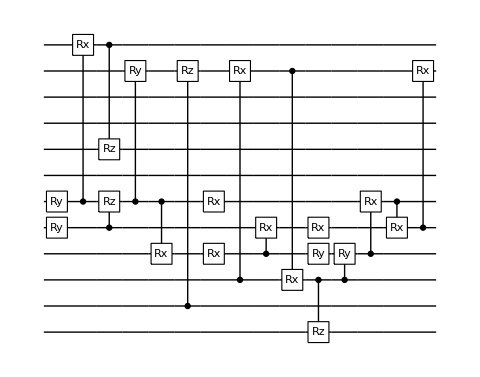

```mathematica
DrawCircuit[ansatz,12]
```

```mathematica
GetCircuitColumns[ansatz]
```

{{Ry_4[θ_195],Ry_5[θ_49]},{C_5[Rx_11[θ_76]]},{C_4[Rz_5[θ_219]],C_11[Rz_7[θ_250]]},{C_5[Ry_10[θ_69]]},{C_5[Rx_3[θ_233]],C_1[Rz_10[θ_243]]},{Rx_5[θ_7],Rx_3[θ_246],C_2[Rx_10[θ_5]]},{C_3[Rx_4[θ_230]],C_10[Rx_2[θ_95]]},{Rx_4[θ_267],Ry_3[θ_278],C_2[Rz_0[θ_164]]},{C_2[Ry_3[θ_275]]},{C_3[Rx_5[θ_4]]},{C_5[Rx_4[θ_113]]},{C_4[Rx_10[θ_123]]}}

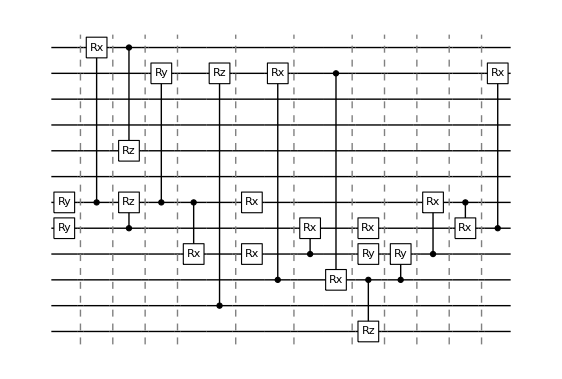

```mathematica
DrawCircuit[GetCircuitColumns[ansatz],12]
```